```mathematica
Clear[n]
f[x_] = Sum[c[k]*e^(-x*k), {k, n}]
```

BellB[n,ⅇ^-x]

```mathematica
BellB[n,ⅇ^-x]
```

BellB[n,ⅇ^-x]

```mathematica
f[2]
```

BellB[n,1/ⅇ^2]

```mathematica
c[k_] = StirlingS2[n,k]
```

StirlingS2[n,k]

```mathematica
f[0.5]
```

BellB[n,0.606531]

```mathematica
f'[x]
```

-ⅇ^-x (-BellB[n,ⅇ^-x]+ⅇ^x BellB[1+n,ⅇ^-x])

```mathematica
e=E
```

ⅇ

```mathematica
f'[x]
```

-ⅇ^-x (-BellB[n,ⅇ^-x]+ⅇ^x BellB[1+n,ⅇ^-x])

```mathematica
f''[x]
```

ⅇ^-x (-BellB[n,ⅇ^-x]+ⅇ^x BellB[1+n,ⅇ^-x])-ⅇ^-x (BellB[1+n,ⅇ^-x]+ⅇ^x BellB[1+n,ⅇ^-x]+ⅇ^-x (-BellB[n,ⅇ^-x]+ⅇ^x BellB[1+n,ⅇ^-x])-ⅇ^x BellB[2+n,ⅇ^-x])

```mathematica
expt[x_] = -f'[x] / f[x]
```

(ⅇ^-x (-BellB[n,ⅇ^-x]+ⅇ^x BellB[1+n,ⅇ^-x]))/BellB[n,ⅇ^-x]

```mathematica
n = 36
```

36

```mathematica
N[expt[0]]
```

12.8409

```mathematica
std[x_] = Sqrt[-expt'[x]]
```

√((ⅇ^-x (-36 ⅇ^(-36 x)-22050 ⅇ^(-35 x)-6251070 ⅇ^(-34 x)-1090508265 ⅇ^(-33 x)-131293244544 ⅇ^(-32 x)-11597846981952 ⅇ^(-31 x)-780191501192400 ⅇ^(-30 x)-40950323061153000 ⅇ^(-29 x)-1704761755293300088 ⅇ^(-28 x)-56919082461989941116 ⅇ^(-27 x)-1535485228185110434596 ⅇ^(-26 x)-33619268343953897718750 ⅇ^(-25 x)-598742764523726037045840 ⅇ^(-24 x)-8675491962496373944276680 ⅇ^(-23 x)-102108548256985969426255440 ⅇ^(-22 x)-972999454835961948670173360 ⅇ^(-21 x)-7469103966408529672901450700 ⅇ^(-20 x)-45874519145067642166437357750 ⅇ^(-19 x)-223465866899244658710537101850 ⅇ^(-18 x)-853913783908229243660575926075 ⅇ^(-17 x)-2525128832215394457669748080096 ⅇ^(-16 x)-5682981931547141531600679178800 ⅇ^(-15 x)-9536521051474908464422670236680 ⅇ^(-14 x)-11633944317667085566743470011860 ⅇ^(-13 x)-9997094123852460373818636658116 ⅇ^(-12 x)-5814337317880563845005333627938 ⅇ^(-11 x)-2174281564503006571275062231150 ⅇ^(-10 x)-488649064824591304467226028625 ⅇ^(-9 x)-60236646073256288484868681464 ⅇ^(-8 x)-3583104579461724773886753708 ⅇ^(-7 x)-85226534496797381707187328 ⅇ^(-6 x)-605346037370757056491500 ⅇ^(-5 x)-786961017456795679604 ⅇ^(-4 x)-75047214569284458 ⅇ^(-3 x)-68719476734 ⅇ^(-2 x)-ⅇ^-x) (-ⅇ^(-36 x)-630 ⅇ^(-35 x)-183855 ⅇ^(-34 x)-33045705 ⅇ^(-33 x)-4102913892 ⅇ^(-32 x)-374124096192 ⅇ^(-31 x)-26006383373080 ⅇ^(-30 x)-1412080105557000 ⅇ^(-29 x)-60884348403332146 ⅇ^(-28 x)-2108114165258886708 ⅇ^(-27 x)-59057124160965785946 ⅇ^(-26 x)-1344770733758155908750 ⅇ^(-25 x)-24947615188488584876910 ⅇ^(-24 x)-377195302717233649751160 ⅇ^(-23 x)-4641297648044816792102520 ⅇ^(-22 x)-46333307373141045174770160 ⅇ^(-21 x)-373455198320426483645072535 ⅇ^(-20 x)-2414448376056191692970387250 ⅇ^(-19 x)-12414770383291369928363172325 ⅇ^(-18 x)-50230222582837014332975054475 ⅇ^(-17 x)-157820552013462153604359255006 ⅇ^(-16 x)-378865462103142768773378611920 ⅇ^(-15 x)-681180075105350604601619302620 ⅇ^(-14 x)-894918793666698889749497693220 ⅇ^(-13 x)-833091176987705031151553054843 ⅇ^(-12 x)-528576119807323985909575784358 ⅇ^(-11 x)-217428156450300657127506223115 ⅇ^(-10 x)-54294340536065700496358447625 ⅇ^(-9 x)-7529580759157036060608585183 ⅇ^(-8 x)-511872082780246396269536244 ⅇ^(-7 x)-14204422416132896951197888 ⅇ^(-6 x)-121069207474151411298300 ⅇ^(-5 x)-196740254364198919901 ⅇ^(-4 x)-25015738189761486 ⅇ^(-3 x)-34359738367 ⅇ^(-2 x)-ⅇ^-x+ⅇ^x (ⅇ^(-37 x)+666 ⅇ^(-36 x)+205905 ⅇ^(-35 x)+39296775 ⅇ^(-34 x)+5193422157 ⅇ^(-33 x)+505417340736 ⅇ^(-32 x)+37604230355032 ⅇ^(-31 x)+2192271606749400 ⅇ^(-30 x)+101834671464485146 ⅇ^(-29 x)+3812875920552186796 ⅇ^(-28 x)+115976206622955727062 ⅇ^(-27 x)+2880255961943266343346 ⅇ^(-26 x)+58566883532442482595660 ⅇ^(-25 x)+975938067240959686797000 ⅇ^(-24 x)+13316789610541190736379200 ⅇ^(-23 x)+148441855630127014601025600 ⅇ^(-22 x)+1346454653156388432315245895 ⅇ^(-21 x)+9883552342464721365871837950 ⅇ^(-20 x)+58289289528359012094800530075 ⅇ^(-19 x)+273696089482081673043512156325 ⅇ^(-18 x)+1011734335921691397264935181081 ⅇ^(-17 x)+2903994294318537226443126692016 ⅇ^(-16 x)+6364162006652492136202298481420 ⅇ^(-15 x)+10431439845141607354172167929900 ⅇ^(-14 x)+12467035494654790597895023066703 ⅇ^(-13 x)+10525670243659784359728212442474 ⅇ^(-12 x)+6031765474330864502132839851053 ⅇ^(-11 x)+2228575905039072271771420678775 ⅇ^(-10 x)+496178645583748340527834613808 ⅇ^(-9 x)+60748518156036534881138217708 ⅇ^(-8 x)+3597309001877857670837951596 ⅇ^(-7 x)+85347603704271533118485628 ⅇ^(-6 x)+605542777625121255411401 ⅇ^(-5 x)+786986033194985441090 ⅇ^(-4 x)+75047248929022825 ⅇ^(-3 x)+68719476735 ⅇ^(-2 x)+ⅇ^-x)))/(ⅇ^(-36 x)+630 ⅇ^(-35 x)+183855 ⅇ^(-34 x)+33045705 ⅇ^(-33 x)+4102913892 ⅇ^(-32 x)+374124096192 ⅇ^(-31 x)+26006383373080 ⅇ^(-30 x)+1412080105557000 ⅇ^(-29 x)+60884348403332146 ⅇ^(-28 x)+2108114165258886708 ⅇ^(-27 x)+59057124160965785946 ⅇ^(-26 x)+1344770733758155908750 ⅇ^(-25 x)+24947615188488584876910 ⅇ^(-24 x)+377195302717233649751160 ⅇ^(-23 x)+4641297648044816792102520 ⅇ^(-22 x)+46333307373141045174770160 ⅇ^(-21 x)+373455198320426483645072535 ⅇ^(-20 x)+2414448376056191692970387250 ⅇ^(-19 x)+12414770383291369928363172325 ⅇ^(-18 x)+50230222582837014332975054475 ⅇ^(-17 x)+157820552013462153604359255006 ⅇ^(-16 x)+378865462103142768773378611920 ⅇ^(-15 x)+681180075105350604601619302620 ⅇ^(-14 x)+894918793666698889749497693220 ⅇ^(-13 x)+833091176987705031151553054843 ⅇ^(-12 x)+528576119807323985909575784358 ⅇ^(-11 x)+217428156450300657127506223115 ⅇ^(-10 x)+54294340536065700496358447625 ⅇ^(-9 x)+7529580759157036060608585183 ⅇ^(-8 x)+511872082780246396269536244 ⅇ^(-7 x)+14204422416132896951197888 ⅇ^(-6 x)+121069207474151411298300 ⅇ^(-5 x)+196740254364198919901 ⅇ^(-4 x)+25015738189761486 ⅇ^(-3 x)+34359738367 ⅇ^(-2 x)+ⅇ^-x)^2+(ⅇ^-x (-ⅇ^(-36 x)-630 ⅇ^(-35 x)-183855 ⅇ^(-34 x)-33045705 ⅇ^(-33 x)-4102913892 ⅇ^(-32 x)-374124096192 ⅇ^(-31 x)-26006383373080 ⅇ^(-30 x)-1412080105557000 ⅇ^(-29 x)-60884348403332146 ⅇ^(-28 x)-2108114165258886708 ⅇ^(-27 x)-59057124160965785946 ⅇ^(-26 x)-1344770733758155908750 ⅇ^(-25 x)-24947615188488584876910 ⅇ^(-24 x)-377195302717233649751160 ⅇ^(-23 x)-4641297648044816792102520 ⅇ^(-22 x)-46333307373141045174770160 ⅇ^(-21 x)-373455198320426483645072535 ⅇ^(-20 x)-2414448376056191692970387250 ⅇ^(-19 x)-12414770383291369928363172325 ⅇ^(-18 x)-50230222582837014332975054475 ⅇ^(-17 x)-157820552013462153604359255006 ⅇ^(-16 x)-378865462103142768773378611920 ⅇ^(-15 x)-681180075105350604601619302620 ⅇ^(-14 x)-894918793666698889749497693220 ⅇ^(-13 x)-833091176987705031151553054843 ⅇ^(-12 x)-528576119807323985909575784358 ⅇ^(-11 x)-217428156450300657127506223115 ⅇ^(-10 x)-54294340536065700496358447625 ⅇ^(-9 x)-7529580759157036060608585183 ⅇ^(-8 x)-511872082780246396269536244 ⅇ^(-7 x)-14204422416132896951197888 ⅇ^(-6 x)-121069207474151411298300 ⅇ^(-5 x)-196740254364198919901 ⅇ^(-4 x)-25015738189761486 ⅇ^(-3 x)-34359738367 ⅇ^(-2 x)-ⅇ^-x+ⅇ^x (ⅇ^(-37 x)+666 ⅇ^(-36 x)+205905 ⅇ^(-35 x)+39296775 ⅇ^(-34 x)+5193422157 ⅇ^(-33 x)+505417340736 ⅇ^(-32 x)+37604230355032 ⅇ^(-31 x)+2192271606749400 ⅇ^(-30 x)+101834671464485146 ⅇ^(-29 x)+3812875920552186796 ⅇ^(-28 x)+115976206622955727062 ⅇ^(-27 x)+2880255961943266343346 ⅇ^(-26 x)+58566883532442482595660 ⅇ^(-25 x)+975938067240959686797000 ⅇ^(-24 x)+13316789610541190736379200 ⅇ^(-23 x)+148441855630127014601025600 ⅇ^(-22 x)+1346454653156388432315245895 ⅇ^(-21 x)+9883552342464721365871837950 ⅇ^(-20 x)+58289289528359012094800530075 ⅇ^(-19 x)+273696089482081673043512156325 ⅇ^(-18 x)+1011734335921691397264935181081 ⅇ^(-17 x)+2903994294318537226443126692016 ⅇ^(-16 x)+6364162006652492136202298481420 ⅇ^(-15 x)+10431439845141607354172167929900 ⅇ^(-14 x)+12467035494654790597895023066703 ⅇ^(-13 x)+10525670243659784359728212442474 ⅇ^(-12 x)+6031765474330864502132839851053 ⅇ^(-11 x)+2228575905039072271771420678775 ⅇ^(-10 x)+496178645583748340527834613808 ⅇ^(-9 x)+60748518156036534881138217708 ⅇ^(-8 x)+3597309001877857670837951596 ⅇ^(-7 x)+85347603704271533118485628 ⅇ^(-6 x)+605542777625121255411401 ⅇ^(-5 x)+786986033194985441090 ⅇ^(-4 x)+75047248929022825 ⅇ^(-3 x)+68719476735 ⅇ^(-2 x)+ⅇ^-x)))/(ⅇ^(-36 x)+630 ⅇ^(-35 x)+183855 ⅇ^(-34 x)+33045705 ⅇ^(-33 x)+4102913892 ⅇ^(-32 x)+374124096192 ⅇ^(-31 x)+26006383373080 ⅇ^(-30 x)+1412080105557000 ⅇ^(-29 x)+60884348403332146 ⅇ^(-28 x)+2108114165258886708 ⅇ^(-27 x)+59057124160965785946 ⅇ^(-26 x)+1344770733758155908750 ⅇ^(-25 x)+24947615188488584876910 ⅇ^(-24 x)+377195302717233649751160 ⅇ^(-23 x)+4641297648044816792102520 ⅇ^(-22 x)+46333307373141045174770160 ⅇ^(-21 x)+373455198320426483645072535 ⅇ^(-20 x)+2414448376056191692970387250 ⅇ^(-19 x)+12414770383291369928363172325 ⅇ^(-18 x)+50230222582837014332975054475 ⅇ^(-17 x)+157820552013462153604359255006 ⅇ^(-16 x)+378865462103142768773378611920 ⅇ^(-15 x)+681180075105350604601619302620 ⅇ^(-14 x)+894918793666698889749497693220 ⅇ^(-13 x)+833091176987705031151553054843 ⅇ^(-12 x)+528576119807323985909575784358 ⅇ^(-11 x)+217428156450300657127506223115 ⅇ^(-10 x)+54294340536065700496358447625 ⅇ^(-9 x)+7529580759157036060608585183 ⅇ^(-8 x)+511872082780246396269536244 ⅇ^(-7 x)+14204422416132896951197888 ⅇ^(-6 x)+121069207474151411298300 ⅇ^(-5 x)+196740254364198919901 ⅇ^(-4 x)+25015738189761486 ⅇ^(-3 x)+34359738367 ⅇ^(-2 x)+ⅇ^-x)-(ⅇ^-x (36 ⅇ^(-36 x)+22050 ⅇ^(-35 x)+6251070 ⅇ^(-34 x)+1090508265 ⅇ^(-33 x)+131293244544 ⅇ^(-32 x)+11597846981952 ⅇ^(-31 x)+780191501192400 ⅇ^(-30 x)+40950323061153000 ⅇ^(-29 x)+1704761755293300088 ⅇ^(-28 x)+56919082461989941116 ⅇ^(-27 x)+1535485228185110434596 ⅇ^(-26 x)+33619268343953897718750 ⅇ^(-25 x)+598742764523726037045840 ⅇ^(-24 x)+8675491962496373944276680 ⅇ^(-23 x)+102108548256985969426255440 ⅇ^(-22 x)+972999454835961948670173360 ⅇ^(-21 x)+7469103966408529672901450700 ⅇ^(-20 x)+45874519145067642166437357750 ⅇ^(-19 x)+223465866899244658710537101850 ⅇ^(-18 x)+853913783908229243660575926075 ⅇ^(-17 x)+2525128832215394457669748080096 ⅇ^(-16 x)+5682981931547141531600679178800 ⅇ^(-15 x)+9536521051474908464422670236680 ⅇ^(-14 x)+11633944317667085566743470011860 ⅇ^(-13 x)+9997094123852460373818636658116 ⅇ^(-12 x)+5814337317880563845005333627938 ⅇ^(-11 x)+2174281564503006571275062231150 ⅇ^(-10 x)+488649064824591304467226028625 ⅇ^(-9 x)+60236646073256288484868681464 ⅇ^(-8 x)+3583104579461724773886753708 ⅇ^(-7 x)+85226534496797381707187328 ⅇ^(-6 x)+605346037370757056491500 ⅇ^(-5 x)+786961017456795679604 ⅇ^(-4 x)+75047214569284458 ⅇ^(-3 x)+68719476734 ⅇ^(-2 x)+ⅇ^-x+ⅇ^x (-37 ⅇ^(-37 x)-23976 ⅇ^(-36 x)-7206675 ⅇ^(-35 x)-1336090350 ⅇ^(-34 x)-171382931181 ⅇ^(-33 x)-16173354903552 ⅇ^(-32 x)-1165731141005992 ⅇ^(-31 x)-65768148202482000 ⅇ^(-30 x)-2953205472470069234 ⅇ^(-29 x)-106760525775461230288 ⅇ^(-28 x)-3131357578819804630674 ⅇ^(-27 x)-74886655010524924926996 ⅇ^(-26 x)-1464172088311062064891500 ⅇ^(-25 x)-23422513613783032483128000 ⅇ^(-24 x)-306286161042447386936721600 ⅇ^(-23 x)-3265720823862794321222563200 ⅇ^(-22 x)-28275547716284157078620163795 ⅇ^(-21 x)-197671046849294427317436759000 ⅇ^(-20 x)-1107496501038821229801210071425 ⅇ^(-19 x)-4926529610677470114783218813850 ⅇ^(-18 x)-17199483710668753753503898078377 ⅇ^(-17 x)-46463908709096595623090027072256 ⅇ^(-16 x)-95462430099787382043034477221300 ⅇ^(-15 x)-146040157831982502958410351018600 ⅇ^(-14 x)-162071461430512277772635299867139 ⅇ^(-13 x)-126308042923917412316738549309688 ⅇ^(-12 x)-66349420217639509523461238361583 ⅇ^(-11 x)-22285759050390722717714206787750 ⅇ^(-10 x)-4465607810253735064750511524272 ⅇ^(-9 x)-485988145248292279049105741664 ⅇ^(-8 x)-25181163013145003695865661172 ⅇ^(-7 x)-512085622225629198710913768 ⅇ^(-6 x)-3027713888125606277057005 ⅇ^(-5 x)-3147944132779941764360 ⅇ^(-4 x)-225141746787068475 ⅇ^(-3 x)-137438953470 ⅇ^(-2 x)-ⅇ^-x)+ⅇ^x (ⅇ^(-37 x)+666 ⅇ^(-36 x)+205905 ⅇ^(-35 x)+39296775 ⅇ^(-34 x)+5193422157 ⅇ^(-33 x)+505417340736 ⅇ^(-32 x)+37604230355032 ⅇ^(-31 x)+2192271606749400 ⅇ^(-30 x)+101834671464485146 ⅇ^(-29 x)+3812875920552186796 ⅇ^(-28 x)+115976206622955727062 ⅇ^(-27 x)+2880255961943266343346 ⅇ^(-26 x)+58566883532442482595660 ⅇ^(-25 x)+975938067240959686797000 ⅇ^(-24 x)+13316789610541190736379200 ⅇ^(-23 x)+148441855630127014601025600 ⅇ^(-22 x)+1346454653156388432315245895 ⅇ^(-21 x)+9883552342464721365871837950 ⅇ^(-20 x)+58289289528359012094800530075 ⅇ^(-19 x)+273696089482081673043512156325 ⅇ^(-18 x)+1011734335921691397264935181081 ⅇ^(-17 x)+2903994294318537226443126692016 ⅇ^(-16 x)+6364162006652492136202298481420 ⅇ^(-15 x)+10431439845141607354172167929900 ⅇ^(-14 x)+12467035494654790597895023066703 ⅇ^(-13 x)+10525670243659784359728212442474 ⅇ^(-12 x)+6031765474330864502132839851053 ⅇ^(-11 x)+2228575905039072271771420678775 ⅇ^(-10 x)+496178645583748340527834613808 ⅇ^(-9 x)+60748518156036534881138217708 ⅇ^(-8 x)+3597309001877857670837951596 ⅇ^(-7 x)+85347603704271533118485628 ⅇ^(-6 x)+605542777625121255411401 ⅇ^(-5 x)+786986033194985441090 ⅇ^(-4 x)+75047248929022825 ⅇ^(-3 x)+68719476735 ⅇ^(-2 x)+ⅇ^-x)))/(ⅇ^(-36 x)+630 ⅇ^(-35 x)+183855 ⅇ^(-34 x)+33045705 ⅇ^(-33 x)+4102913892 ⅇ^(-32 x)+374124096192 ⅇ^(-31 x)+26006383373080 ⅇ^(-30 x)+1412080105557000 ⅇ^(-29 x)+60884348403332146 ⅇ^(-28 x)+2108114165258886708 ⅇ^(-27 x)+59057124160965785946 ⅇ^(-26 x)+1344770733758155908750 ⅇ^(-25 x)+24947615188488584876910 ⅇ^(-24 x)+377195302717233649751160 ⅇ^(-23 x)+4641297648044816792102520 ⅇ^(-22 x)+46333307373141045174770160 ⅇ^(-21 x)+373455198320426483645072535 ⅇ^(-20 x)+2414448376056191692970387250 ⅇ^(-19 x)+12414770383291369928363172325 ⅇ^(-18 x)+50230222582837014332975054475 ⅇ^(-17 x)+157820552013462153604359255006 ⅇ^(-16 x)+378865462103142768773378611920 ⅇ^(-15 x)+681180075105350604601619302620 ⅇ^(-14 x)+894918793666698889749497693220 ⅇ^(-13 x)+833091176987705031151553054843 ⅇ^(-12 x)+528576119807323985909575784358 ⅇ^(-11 x)+217428156450300657127506223115 ⅇ^(-10 x)+54294340536065700496358447625 ⅇ^(-9 x)+7529580759157036060608585183 ⅇ^(-8 x)+511872082780246396269536244 ⅇ^(-7 x)+14204422416132896951197888 ⅇ^(-6 x)+121069207474151411298300 ⅇ^(-5 x)+196740254364198919901 ⅇ^(-4 x)+25015738189761486 ⅇ^(-3 x)+34359738367 ⅇ^(-2 x)+ⅇ^-x))

```mathematica
N[std[0]]
```

1.67552

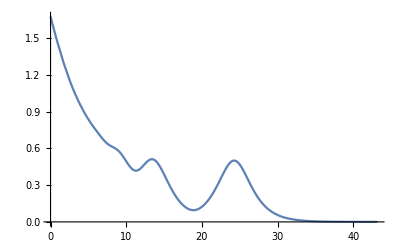

```mathematica
Plot[std[x],{x,0,1.2*n}]
```

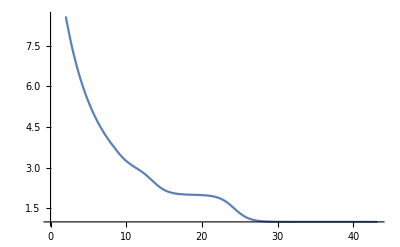

```mathematica
Plot[expt[x],{x,0,1.2*n}]
```

```mathematica
FindRoot[expt[x]==1.5,{x,10}]
```

{x→24.2602}

```mathematica
N[expt[24.26021488099619]]
```

1.5

```mathematica
var[x_] = -expt'[x]
```

(ⅇ^-x (-36 ⅇ^(-36 x)-22050 ⅇ^(-35 x)-6251070 ⅇ^(-34 x)-1090508265 ⅇ^(-33 x)-131293244544 ⅇ^(-32 x)-11597846981952 ⅇ^(-31 x)-780191501192400 ⅇ^(-30 x)-40950323061153000 ⅇ^(-29 x)-1704761755293300088 ⅇ^(-28 x)-56919082461989941116 ⅇ^(-27 x)-1535485228185110434596 ⅇ^(-26 x)-33619268343953897718750 ⅇ^(-25 x)-598742764523726037045840 ⅇ^(-24 x)-8675491962496373944276680 ⅇ^(-23 x)-102108548256985969426255440 ⅇ^(-22 x)-972999454835961948670173360 ⅇ^(-21 x)-7469103966408529672901450700 ⅇ^(-20 x)-45874519145067642166437357750 ⅇ^(-19 x)-223465866899244658710537101850 ⅇ^(-18 x)-853913783908229243660575926075 ⅇ^(-17 x)-2525128832215394457669748080096 ⅇ^(-16 x)-5682981931547141531600679178800 ⅇ^(-15 x)-9536521051474908464422670236680 ⅇ^(-14 x)-11633944317667085566743470011860 ⅇ^(-13 x)-9997094123852460373818636658116 ⅇ^(-12 x)-5814337317880563845005333627938 ⅇ^(-11 x)-2174281564503006571275062231150 ⅇ^(-10 x)-488649064824591304467226028625 ⅇ^(-9 x)-60236646073256288484868681464 ⅇ^(-8 x)-3583104579461724773886753708 ⅇ^(-7 x)-85226534496797381707187328 ⅇ^(-6 x)-605346037370757056491500 ⅇ^(-5 x)-786961017456795679604 ⅇ^(-4 x)-75047214569284458 ⅇ^(-3 x)-68719476734 ⅇ^(-2 x)-ⅇ^-x) (-ⅇ^(-36 x)-630 ⅇ^(-35 x)-183855 ⅇ^(-34 x)-33045705 ⅇ^(-33 x)-4102913892 ⅇ^(-32 x)-374124096192 ⅇ^(-31 x)-26006383373080 ⅇ^(-30 x)-1412080105557000 ⅇ^(-29 x)-60884348403332146 ⅇ^(-28 x)-2108114165258886708 ⅇ^(-27 x)-59057124160965785946 ⅇ^(-26 x)-1344770733758155908750 ⅇ^(-25 x)-24947615188488584876910 ⅇ^(-24 x)-377195302717233649751160 ⅇ^(-23 x)-4641297648044816792102520 ⅇ^(-22 x)-46333307373141045174770160 ⅇ^(-21 x)-373455198320426483645072535 ⅇ^(-20 x)-2414448376056191692970387250 ⅇ^(-19 x)-12414770383291369928363172325 ⅇ^(-18 x)-50230222582837014332975054475 ⅇ^(-17 x)-157820552013462153604359255006 ⅇ^(-16 x)-378865462103142768773378611920 ⅇ^(-15 x)-681180075105350604601619302620 ⅇ^(-14 x)-894918793666698889749497693220 ⅇ^(-13 x)-833091176987705031151553054843 ⅇ^(-12 x)-528576119807323985909575784358 ⅇ^(-11 x)-217428156450300657127506223115 ⅇ^(-10 x)-54294340536065700496358447625 ⅇ^(-9 x)-7529580759157036060608585183 ⅇ^(-8 x)-511872082780246396269536244 ⅇ^(-7 x)-14204422416132896951197888 ⅇ^(-6 x)-121069207474151411298300 ⅇ^(-5 x)-196740254364198919901 ⅇ^(-4 x)-25015738189761486 ⅇ^(-3 x)-34359738367 ⅇ^(-2 x)-ⅇ^-x+ⅇ^x (ⅇ^(-37 x)+666 ⅇ^(-36 x)+205905 ⅇ^(-35 x)+39296775 ⅇ^(-34 x)+5193422157 ⅇ^(-33 x)+505417340736 ⅇ^(-32 x)+37604230355032 ⅇ^(-31 x)+2192271606749400 ⅇ^(-30 x)+101834671464485146 ⅇ^(-29 x)+3812875920552186796 ⅇ^(-28 x)+115976206622955727062 ⅇ^(-27 x)+2880255961943266343346 ⅇ^(-26 x)+58566883532442482595660 ⅇ^(-25 x)+975938067240959686797000 ⅇ^(-24 x)+13316789610541190736379200 ⅇ^(-23 x)+148441855630127014601025600 ⅇ^(-22 x)+1346454653156388432315245895 ⅇ^(-21 x)+9883552342464721365871837950 ⅇ^(-20 x)+58289289528359012094800530075 ⅇ^(-19 x)+273696089482081673043512156325 ⅇ^(-18 x)+1011734335921691397264935181081 ⅇ^(-17 x)+2903994294318537226443126692016 ⅇ^(-16 x)+6364162006652492136202298481420 ⅇ^(-15 x)+10431439845141607354172167929900 ⅇ^(-14 x)+12467035494654790597895023066703 ⅇ^(-13 x)+10525670243659784359728212442474 ⅇ^(-12 x)+6031765474330864502132839851053 ⅇ^(-11 x)+2228575905039072271771420678775 ⅇ^(-10 x)+496178645583748340527834613808 ⅇ^(-9 x)+60748518156036534881138217708 ⅇ^(-8 x)+3597309001877857670837951596 ⅇ^(-7 x)+85347603704271533118485628 ⅇ^(-6 x)+605542777625121255411401 ⅇ^(-5 x)+786986033194985441090 ⅇ^(-4 x)+75047248929022825 ⅇ^(-3 x)+68719476735 ⅇ^(-2 x)+ⅇ^-x)))/(ⅇ^(-36 x)+630 ⅇ^(-35 x)+183855 ⅇ^(-34 x)+33045705 ⅇ^(-33 x)+4102913892 ⅇ^(-32 x)+374124096192 ⅇ^(-31 x)+26006383373080 ⅇ^(-30 x)+1412080105557000 ⅇ^(-29 x)+60884348403332146 ⅇ^(-28 x)+2108114165258886708 ⅇ^(-27 x)+59057124160965785946 ⅇ^(-26 x)+1344770733758155908750 ⅇ^(-25 x)+24947615188488584876910 ⅇ^(-24 x)+377195302717233649751160 ⅇ^(-23 x)+4641297648044816792102520 ⅇ^(-22 x)+46333307373141045174770160 ⅇ^(-21 x)+373455198320426483645072535 ⅇ^(-20 x)+2414448376056191692970387250 ⅇ^(-19 x)+12414770383291369928363172325 ⅇ^(-18 x)+50230222582837014332975054475 ⅇ^(-17 x)+157820552013462153604359255006 ⅇ^(-16 x)+378865462103142768773378611920 ⅇ^(-15 x)+681180075105350604601619302620 ⅇ^(-14 x)+894918793666698889749497693220 ⅇ^(-13 x)+833091176987705031151553054843 ⅇ^(-12 x)+528576119807323985909575784358 ⅇ^(-11 x)+217428156450300657127506223115 ⅇ^(-10 x)+54294340536065700496358447625 ⅇ^(-9 x)+7529580759157036060608585183 ⅇ^(-8 x)+511872082780246396269536244 ⅇ^(-7 x)+14204422416132896951197888 ⅇ^(-6 x)+121069207474151411298300 ⅇ^(-5 x)+196740254364198919901 ⅇ^(-4 x)+25015738189761486 ⅇ^(-3 x)+34359738367 ⅇ^(-2 x)+ⅇ^-x)^2+(ⅇ^-x (-ⅇ^(-36 x)-630 ⅇ^(-35 x)-183855 ⅇ^(-34 x)-33045705 ⅇ^(-33 x)-4102913892 ⅇ^(-32 x)-374124096192 ⅇ^(-31 x)-26006383373080 ⅇ^(-30 x)-1412080105557000 ⅇ^(-29 x)-60884348403332146 ⅇ^(-28 x)-2108114165258886708 ⅇ^(-27 x)-59057124160965785946 ⅇ^(-26 x)-1344770733758155908750 ⅇ^(-25 x)-24947615188488584876910 ⅇ^(-24 x)-377195302717233649751160 ⅇ^(-23 x)-4641297648044816792102520 ⅇ^(-22 x)-46333307373141045174770160 ⅇ^(-21 x)-373455198320426483645072535 ⅇ^(-20 x)-2414448376056191692970387250 ⅇ^(-19 x)-12414770383291369928363172325 ⅇ^(-18 x)-50230222582837014332975054475 ⅇ^(-17 x)-157820552013462153604359255006 ⅇ^(-16 x)-378865462103142768773378611920 ⅇ^(-15 x)-681180075105350604601619302620 ⅇ^(-14 x)-894918793666698889749497693220 ⅇ^(-13 x)-833091176987705031151553054843 ⅇ^(-12 x)-528576119807323985909575784358 ⅇ^(-11 x)-217428156450300657127506223115 ⅇ^(-10 x)-54294340536065700496358447625 ⅇ^(-9 x)-7529580759157036060608585183 ⅇ^(-8 x)-511872082780246396269536244 ⅇ^(-7 x)-14204422416132896951197888 ⅇ^(-6 x)-121069207474151411298300 ⅇ^(-5 x)-196740254364198919901 ⅇ^(-4 x)-25015738189761486 ⅇ^(-3 x)-34359738367 ⅇ^(-2 x)-ⅇ^-x+ⅇ^x (ⅇ^(-37 x)+666 ⅇ^(-36 x)+205905 ⅇ^(-35 x)+39296775 ⅇ^(-34 x)+5193422157 ⅇ^(-33 x)+505417340736 ⅇ^(-32 x)+37604230355032 ⅇ^(-31 x)+2192271606749400 ⅇ^(-30 x)+101834671464485146 ⅇ^(-29 x)+3812875920552186796 ⅇ^(-28 x)+115976206622955727062 ⅇ^(-27 x)+2880255961943266343346 ⅇ^(-26 x)+58566883532442482595660 ⅇ^(-25 x)+975938067240959686797000 ⅇ^(-24 x)+13316789610541190736379200 ⅇ^(-23 x)+148441855630127014601025600 ⅇ^(-22 x)+1346454653156388432315245895 ⅇ^(-21 x)+9883552342464721365871837950 ⅇ^(-20 x)+58289289528359012094800530075 ⅇ^(-19 x)+273696089482081673043512156325 ⅇ^(-18 x)+1011734335921691397264935181081 ⅇ^(-17 x)+2903994294318537226443126692016 ⅇ^(-16 x)+6364162006652492136202298481420 ⅇ^(-15 x)+10431439845141607354172167929900 ⅇ^(-14 x)+12467035494654790597895023066703 ⅇ^(-13 x)+10525670243659784359728212442474 ⅇ^(-12 x)+6031765474330864502132839851053 ⅇ^(-11 x)+2228575905039072271771420678775 ⅇ^(-10 x)+496178645583748340527834613808 ⅇ^(-9 x)+60748518156036534881138217708 ⅇ^(-8 x)+3597309001877857670837951596 ⅇ^(-7 x)+85347603704271533118485628 ⅇ^(-6 x)+605542777625121255411401 ⅇ^(-5 x)+786986033194985441090 ⅇ^(-4 x)+75047248929022825 ⅇ^(-3 x)+68719476735 ⅇ^(-2 x)+ⅇ^-x)))/(ⅇ^(-36 x)+630 ⅇ^(-35 x)+183855 ⅇ^(-34 x)+33045705 ⅇ^(-33 x)+4102913892 ⅇ^(-32 x)+374124096192 ⅇ^(-31 x)+26006383373080 ⅇ^(-30 x)+1412080105557000 ⅇ^(-29 x)+60884348403332146 ⅇ^(-28 x)+2108114165258886708 ⅇ^(-27 x)+59057124160965785946 ⅇ^(-26 x)+1344770733758155908750 ⅇ^(-25 x)+24947615188488584876910 ⅇ^(-24 x)+377195302717233649751160 ⅇ^(-23 x)+4641297648044816792102520 ⅇ^(-22 x)+46333307373141045174770160 ⅇ^(-21 x)+373455198320426483645072535 ⅇ^(-20 x)+2414448376056191692970387250 ⅇ^(-19 x)+12414770383291369928363172325 ⅇ^(-18 x)+50230222582837014332975054475 ⅇ^(-17 x)+157820552013462153604359255006 ⅇ^(-16 x)+378865462103142768773378611920 ⅇ^(-15 x)+681180075105350604601619302620 ⅇ^(-14 x)+894918793666698889749497693220 ⅇ^(-13 x)+833091176987705031151553054843 ⅇ^(-12 x)+528576119807323985909575784358 ⅇ^(-11 x)+217428156450300657127506223115 ⅇ^(-10 x)+54294340536065700496358447625 ⅇ^(-9 x)+7529580759157036060608585183 ⅇ^(-8 x)+511872082780246396269536244 ⅇ^(-7 x)+14204422416132896951197888 ⅇ^(-6 x)+121069207474151411298300 ⅇ^(-5 x)+196740254364198919901 ⅇ^(-4 x)+25015738189761486 ⅇ^(-3 x)+34359738367 ⅇ^(-2 x)+ⅇ^-x)-(ⅇ^-x (36 ⅇ^(-36 x)+22050 ⅇ^(-35 x)+6251070 ⅇ^(-34 x)+1090508265 ⅇ^(-33 x)+131293244544 ⅇ^(-32 x)+11597846981952 ⅇ^(-31 x)+780191501192400 ⅇ^(-30 x)+40950323061153000 ⅇ^(-29 x)+1704761755293300088 ⅇ^(-28 x)+56919082461989941116 ⅇ^(-27 x)+1535485228185110434596 ⅇ^(-26 x)+33619268343953897718750 ⅇ^(-25 x)+598742764523726037045840 ⅇ^(-24 x)+8675491962496373944276680 ⅇ^(-23 x)+102108548256985969426255440 ⅇ^(-22 x)+972999454835961948670173360 ⅇ^(-21 x)+7469103966408529672901450700 ⅇ^(-20 x)+45874519145067642166437357750 ⅇ^(-19 x)+223465866899244658710537101850 ⅇ^(-18 x)+853913783908229243660575926075 ⅇ^(-17 x)+2525128832215394457669748080096 ⅇ^(-16 x)+5682981931547141531600679178800 ⅇ^(-15 x)+9536521051474908464422670236680 ⅇ^(-14 x)+11633944317667085566743470011860 ⅇ^(-13 x)+9997094123852460373818636658116 ⅇ^(-12 x)+5814337317880563845005333627938 ⅇ^(-11 x)+2174281564503006571275062231150 ⅇ^(-10 x)+488649064824591304467226028625 ⅇ^(-9 x)+60236646073256288484868681464 ⅇ^(-8 x)+3583104579461724773886753708 ⅇ^(-7 x)+85226534496797381707187328 ⅇ^(-6 x)+605346037370757056491500 ⅇ^(-5 x)+786961017456795679604 ⅇ^(-4 x)+75047214569284458 ⅇ^(-3 x)+68719476734 ⅇ^(-2 x)+ⅇ^-x+ⅇ^x (-37 ⅇ^(-37 x)-23976 ⅇ^(-36 x)-7206675 ⅇ^(-35 x)-1336090350 ⅇ^(-34 x)-171382931181 ⅇ^(-33 x)-16173354903552 ⅇ^(-32 x)-1165731141005992 ⅇ^(-31 x)-65768148202482000 ⅇ^(-30 x)-2953205472470069234 ⅇ^(-29 x)-106760525775461230288 ⅇ^(-28 x)-3131357578819804630674 ⅇ^(-27 x)-74886655010524924926996 ⅇ^(-26 x)-1464172088311062064891500 ⅇ^(-25 x)-23422513613783032483128000 ⅇ^(-24 x)-306286161042447386936721600 ⅇ^(-23 x)-3265720823862794321222563200 ⅇ^(-22 x)-28275547716284157078620163795 ⅇ^(-21 x)-197671046849294427317436759000 ⅇ^(-20 x)-1107496501038821229801210071425 ⅇ^(-19 x)-4926529610677470114783218813850 ⅇ^(-18 x)-17199483710668753753503898078377 ⅇ^(-17 x)-46463908709096595623090027072256 ⅇ^(-16 x)-95462430099787382043034477221300 ⅇ^(-15 x)-146040157831982502958410351018600 ⅇ^(-14 x)-162071461430512277772635299867139 ⅇ^(-13 x)-126308042923917412316738549309688 ⅇ^(-12 x)-66349420217639509523461238361583 ⅇ^(-11 x)-22285759050390722717714206787750 ⅇ^(-10 x)-4465607810253735064750511524272 ⅇ^(-9 x)-485988145248292279049105741664 ⅇ^(-8 x)-25181163013145003695865661172 ⅇ^(-7 x)-512085622225629198710913768 ⅇ^(-6 x)-3027713888125606277057005 ⅇ^(-5 x)-3147944132779941764360 ⅇ^(-4 x)-225141746787068475 ⅇ^(-3 x)-137438953470 ⅇ^(-2 x)-ⅇ^-x)+ⅇ^x (ⅇ^(-37 x)+666 ⅇ^(-36 x)+205905 ⅇ^(-35 x)+39296775 ⅇ^(-34 x)+5193422157 ⅇ^(-33 x)+505417340736 ⅇ^(-32 x)+37604230355032 ⅇ^(-31 x)+2192271606749400 ⅇ^(-30 x)+101834671464485146 ⅇ^(-29 x)+3812875920552186796 ⅇ^(-28 x)+115976206622955727062 ⅇ^(-27 x)+2880255961943266343346 ⅇ^(-26 x)+58566883532442482595660 ⅇ^(-25 x)+975938067240959686797000 ⅇ^(-24 x)+13316789610541190736379200 ⅇ^(-23 x)+148441855630127014601025600 ⅇ^(-22 x)+1346454653156388432315245895 ⅇ^(-21 x)+9883552342464721365871837950 ⅇ^(-20 x)+58289289528359012094800530075 ⅇ^(-19 x)+273696089482081673043512156325 ⅇ^(-18 x)+1011734335921691397264935181081 ⅇ^(-17 x)+2903994294318537226443126692016 ⅇ^(-16 x)+6364162006652492136202298481420 ⅇ^(-15 x)+10431439845141607354172167929900 ⅇ^(-14 x)+12467035494654790597895023066703 ⅇ^(-13 x)+10525670243659784359728212442474 ⅇ^(-12 x)+6031765474330864502132839851053 ⅇ^(-11 x)+2228575905039072271771420678775 ⅇ^(-10 x)+496178645583748340527834613808 ⅇ^(-9 x)+60748518156036534881138217708 ⅇ^(-8 x)+3597309001877857670837951596 ⅇ^(-7 x)+85347603704271533118485628 ⅇ^(-6 x)+605542777625121255411401 ⅇ^(-5 x)+786986033194985441090 ⅇ^(-4 x)+75047248929022825 ⅇ^(-3 x)+68719476735 ⅇ^(-2 x)+ⅇ^-x)))/(ⅇ^(-36 x)+630 ⅇ^(-35 x)+183855 ⅇ^(-34 x)+33045705 ⅇ^(-33 x)+4102913892 ⅇ^(-32 x)+374124096192 ⅇ^(-31 x)+26006383373080 ⅇ^(-30 x)+1412080105557000 ⅇ^(-29 x)+60884348403332146 ⅇ^(-28 x)+2108114165258886708 ⅇ^(-27 x)+59057124160965785946 ⅇ^(-26 x)+1344770733758155908750 ⅇ^(-25 x)+24947615188488584876910 ⅇ^(-24 x)+377195302717233649751160 ⅇ^(-23 x)+4641297648044816792102520 ⅇ^(-22 x)+46333307373141045174770160 ⅇ^(-21 x)+373455198320426483645072535 ⅇ^(-20 x)+2414448376056191692970387250 ⅇ^(-19 x)+12414770383291369928363172325 ⅇ^(-18 x)+50230222582837014332975054475 ⅇ^(-17 x)+157820552013462153604359255006 ⅇ^(-16 x)+378865462103142768773378611920 ⅇ^(-15 x)+681180075105350604601619302620 ⅇ^(-14 x)+894918793666698889749497693220 ⅇ^(-13 x)+833091176987705031151553054843 ⅇ^(-12 x)+528576119807323985909575784358 ⅇ^(-11 x)+217428156450300657127506223115 ⅇ^(-10 x)+54294340536065700496358447625 ⅇ^(-9 x)+7529580759157036060608585183 ⅇ^(-8 x)+511872082780246396269536244 ⅇ^(-7 x)+14204422416132896951197888 ⅇ^(-6 x)+121069207474151411298300 ⅇ^(-5 x)+196740254364198919901 ⅇ^(-4 x)+25015738189761486 ⅇ^(-3 x)+34359738367 ⅇ^(-2 x)+ⅇ^-x)

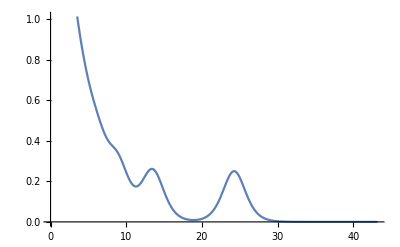

```mathematica
Plot[var[x],{x,0,1.2n}]
```

```mathematica
FindRoot[var'[x], {x,24}]
```

General::munfl: Exp[-864.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-840.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-816.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{x→24.26}

```mathematica
expt[24.2599605946836]
```

1.50006

```mathematica
expt[83.18]
```

1.49942

```mathematica
expt[83.01]
```

1.54182

```mathematica
NMaximize[{var[x],23<x<25},x]
```

{0.250021,{x→24.26}}